### Vector definitions

```mathematica
S1 = {S1x[t],S1y[t],S1z[t]};
S2 = {S2x[t],-S1y[t],S2z[t]};
J={0,0,Jz};
```

```mathematica
L=J-S1-S2;
```

```mathematica
(*S0=(1+1/q)S1+(1+q)S2;*)
```

```mathematica
(*λ=Dot[L,S0]/Norm[L]^2;*)
```

### Differential equations

```mathematica
dS1=Simplify[Cross[1/(2 d^3)((4+3/q-3/(q+1)λ)L+S2),S1]]
dS2=Simplify[Cross[1/(2 d^3)((4+3q-(3q)/(q+2)λ)L+S1),S2]]
fprime={S1x'[t],S1y'[t],S1z'[t],S2x'[t],S2y'[t],S2z'[t]};
```

{(S1y[t] (-2 (3+7 q+4 q^2-3 q λ)+3 (1+q^2-q (-2+λ)) S1z[t]+3 (1+2 q+q^2-q λ) S2z[t]))/(2 d^3 q (1+q)),(3 (1+q^2-q (-2+λ)) S1z[t] S2x[t]+S1x[t] (6+14 q+8 q^2-6 q λ-3 (1+2 q+q^2-q λ) S2z[t]))/(2 d^3 q (1+q)),-(3 (1+q^2-q (-2+λ)) S1y[t] (S1x[t]+S2x[t]))/(2 d^3 q (1+q))}

{-(S1y[t] (-2 (8+10 q+3 q^2-3 q λ)+3 (2+q^2-q (-3+λ)) S1z[t]+3 (2+3 q+q^2-q λ) S2z[t]))/(2 d^3 (2+q)),((16+20 q+6 q^2-6 q λ-3 (2+3 q+q^2-q λ) S1z[t]) S2x[t]+3 (2+q^2-q (-3+λ)) S1x[t] S2z[t])/(2 d^3 (2+q)),(3 (2+q^2-q (-3+λ)) S1y[t] (S1x[t]+S2x[t]))/(2 d^3 (2+q))}

### Numerical solution

```mathematica
Jz=2;
solution=With[{Jz=Jz,d=1,q=0.6,λ=0.15},NDSolve[{
S1x'[t]==(S1y[t] (-Jz (3+7 q+4 q^2-3 q λ)+3 (1+q^2-q (-2+λ)) S1z[t]+3 (1+2 q+q^2-q λ) S2z[t]))/(2 d^3 q (1+q)),S1y'[t]==(3 (1+q^2-q (-2+λ)) S1z[t] S2x[t]+S1x[t] (Jz (3+7 q+4 q^2-3 q λ)-3 (1+2 q+q^2-q λ) S2z[t]))/(2 d^3 q (1+q)),S1z'[t]==-(3 (1+q^2-q (-2+λ)) S1y[t] (S1x[t]+S2x[t]))/(2 d^3 q (1+q)),S2x'[t]==(S1y[t] (Jz (8+10 q+3 q^2-3 q λ)-3 (2+q^2-q (-3+λ)) S1z[t]-3 (2+3 q+q^2-q λ) S2z[t]))/(2 d^3 (2+q)),S2y'[t]==((Jz (8+10 q+3 q^2-3 q λ)-3 (2+3 q+q^2-q λ) S1z[t]) S2x[t]+3 (2+q^2-q (-3+λ)) S1x[t] S2z[t])/(2 d^3 (2+q)),S2z'[t]==(3 (2+q^2-q (-3+λ)) S1y[t] (S1x[t]+S2x[t]))/(2 d^3 (2+q)),
S1x[0]==0.01,S1y[0]==0.001,S1z[0]==0.01,S2x[0]==0.05,S2y[0]==-S1y[0],S2z[0]==0.01},{S1x,S1y,S1z,S2x,S2y,S2z},{t,0,30}]];
```

```mathematica
S1v[t_]:={S1x[t],S1y[t],S1z[t]}/. solution[[1]]
S2v[t_]:={S2x[t],-S1y[t],S2z[t]}/. solution[[1]]
Jv[t_]:={0,0,Jz};
Lv[t_]:=Jv[t]-S1v[t]-S2v[t];
Sv[t_]:=S1v[t]+S2v[t];
```

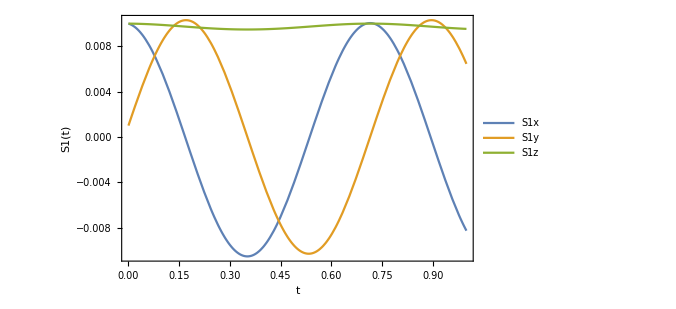

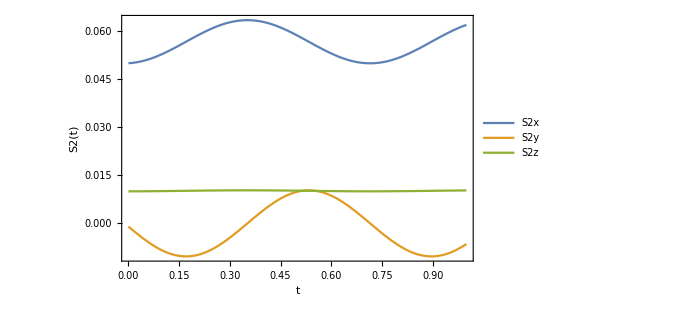

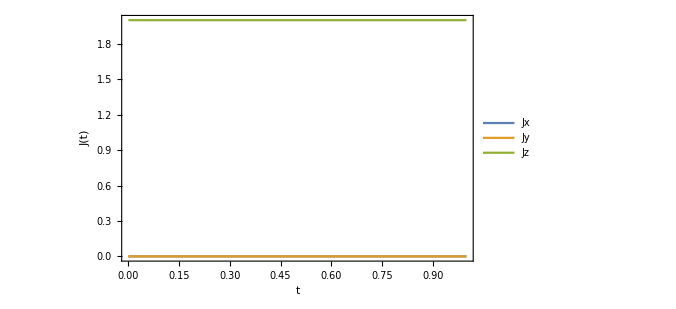

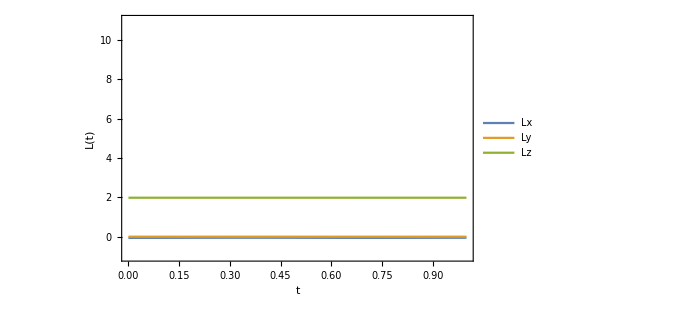

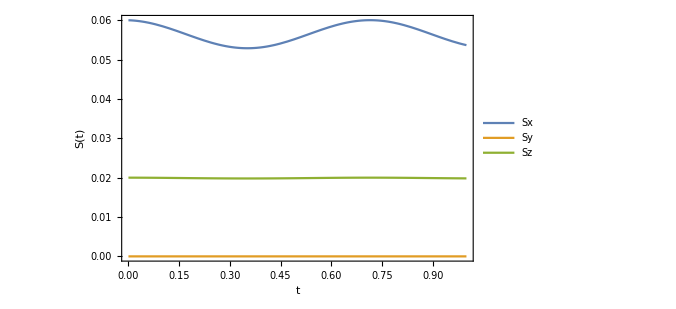

```mathematica
Plot[Evaluate[S1v[t]/. solution],{t,0,1},Frame->True,FrameLabel->{"t","S1(t)"},PlotLegends->Placed[{"S1x","S1y","S1z"},{Scaled[{0.1,1}],{-1,1}}],PlotRange->All,WorkingPrecision->MachinePrecision,ImageSize->500]
Plot[Evaluate[S2v[t]/. solution],{t,0,1},Frame->True,FrameLabel->{"t","S2(t)"},PlotLegends->Placed[{"S2x","S2y","S2z"},{Scaled[{0.1,1}],{-1,1}}],PlotRange->All,WorkingPrecision->MachinePrecision,ImageSize->500]
Plot[Evaluate[Jv[t]/. solution],{t,0,1},Frame->True,FrameLabel->{"t","J(t)"},PlotLegends->Placed[{"Jx","Jy","Jz"},{Scaled[{0.1,1}],{-1,1}}],PlotRange->All,WorkingPrecision->MachinePrecision,ImageSize->500]
Plot[Evaluate[Lv[t]/. solution],{t,0,1},Frame->True,FrameLabel->{"t","L(t)"},PlotLegends->Placed[{"Lx","Ly","Lz"},{Scaled[{0.1,1}],{-1,1}}],PlotRange->{{0,1},{-1,11}},WorkingPrecision->MachinePrecision,ImageSize->500]
Plot[Evaluate[Sv[t]/. solution],{t,0,1},Frame->True,FrameLabel->{"t","S(t)"},PlotLegends->Placed[{"Sx","Sy","Sz"},{Scaled[{0.1,1}],{-1,1}}],PlotRange->All,WorkingPrecision->MachinePrecision,ImageSize->500]
```

```mathematica
NormS1[t_]:=Norm[S1v[t]];
NormS2[t_]:=Norm[S2v[t]];
NormJ[t_]:=Norm[Jv[t]];
NormL[t_]:=Norm[Lv[t]];
NormS[t_]:=Norm[Sv[t]];
```

```mathematica
S1u[t_]:=S1v[t]/NormS1[t];
Su[t_]:=Sv[t]/NormS[t];
```

```mathematica
cosθL[t_]:=(NormJ[t]^2+NormL[t]^2-NormS[t]^2)/(2NormJ[t]NormL[t]);
sinθL[t_]:=(Lv[t][[1]])/NormL[t];
```

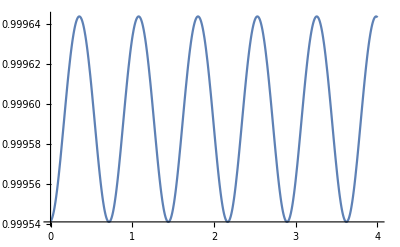

```mathematica
Plot[{cosθL[t]},{t,0,4}, PlotLegends->"Expressions"]
```

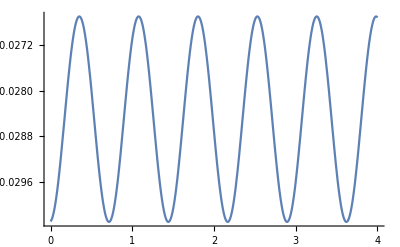

```mathematica
Plot[{sinθL[t]},{t,0,4}, PlotLegends->"Expressions"]
```

```mathematica
SO[t_]:={(NormJ[t]-NormL[t]cosθL[t])/NormS[t],0,(NormL[t]sinθL[t])/NormS[t]};
```

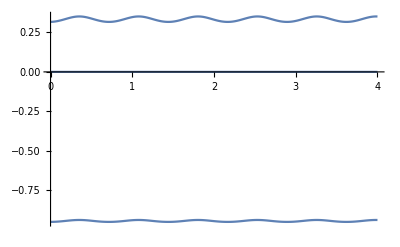

```mathematica
Plot[SO[t],{t,0,4},PlotRange->All]
```

```mathematica
DotProduct1[t_]:=Dot[S1u[t],SO[t]];
CrossProduct1[t_]:=Cross[S1u[t],Su[t]];
NormCross1[t_]:=Norm[CrossProduct1[t]];
```

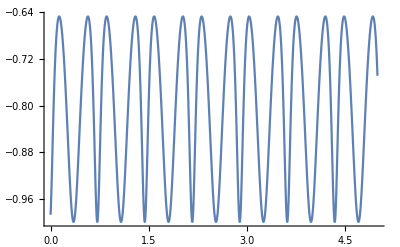

```mathematica
cosϕ[t_]:=DotProduct1[t]/NormCross1[t];
Plot[cosϕ[t],{t,0,5},PlotRange->All]
```